## Displaying Lists

ListPlot is one way to display, or visualize, a list of numbers. There are lots of others. Different ones tend to emphasize different features of a list.

ListLinePlot plots a list, joining up values:

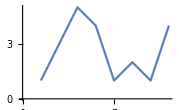

```mathematica
ListLinePlot[{1,3,5,4,1,2,1,4}]
```

When values jump around, it’s usually harder to understand if you don’t join them up:

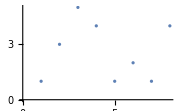

```mathematica
ListPlot[{1,3,5,4,1,2,1,4}]
```

Making a bar chart can be useful too:

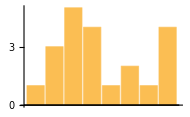

```mathematica
BarChart[{1,3,5,4,1,2,1,4}]
```

So long as the list isn’t too long, a pie chart can be useful:

```mathematica
PieChart[{1,3,5,4}]
```

-Graphics-

If you just want to know which numbers appear, you can plot them on a number line:

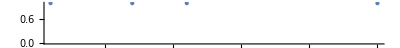

```mathematica
NumberLinePlot[{1,7,11,25}]
```

Sometimes you don’t want a plot at all; you just want to put the elements of a list in a column:

```mathematica
Column[{100,350,502,400}]
```

100
350
502
400

Lists can contain anything, including graphics. So you can combine plots by putting them in lists.

Make a list of two pie charts:

```mathematica
{PieChart[Range[3]],PieChart[Range[5]]}
```

{-Graphics-,-Graphics-}

Show three bar charts together:

```mathematica
{BarChart[{1,1,4,2}],BarChart[{5,1,1,0}],BarChart[{1,3,2,4}]}
```

{-Graphics-,-Graphics-,-Graphics-}

Vocabulary

ListLinePlot[{1,2,5}] |   | values joined by a line 
BarChart[{1,2,5}] |   | bar chart (values give bar heights) 
PieChart[{1,2,5}] |   | pie chart (values give wedge sizes) 
NumberLinePlot[{1,2,5}] |   | numbers arranged on a line 
Column[{1,2,5}] |   | elements displayed in a column

"7 Exercises Available"
"with 6 extras" | "Get Started »"

Make a bar chart of {1,1,2,3,5}. »

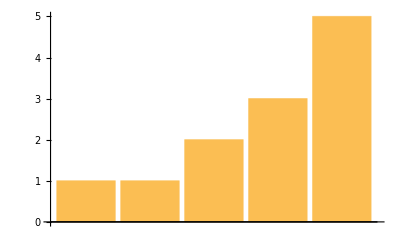
| Expected output: |  
  | -Graphics- |

Make a pie chart of numbers from 1 to 10. »

| Expected output: |  
  | -Graphics- |

Make a bar chart of numbers counting down from 20 to 1. »

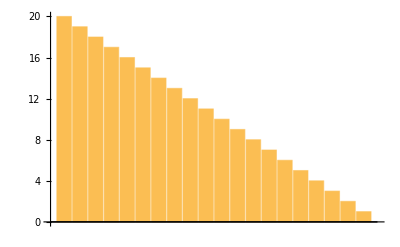
| Expected output: |  
  | -Graphics- |

Display numbers from 1 to 5 in a column. »

| Expected output: |  
  | 1
2
3
4
5 |

Make a number line plot of the squares {1,4,9,16,25}. »

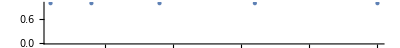
| Expected output: |  
  | -Graphics- |

Make a pie chart with 10 identical segments, each of size 1. »

| Expected output: |  
  | -Graphics- |

Make a column of pie charts with 1, 2 and 3 identical segments. »

| Expected output: |  
  | -Graphics- |

Make a list of pie charts with 1, 2 and 3 identical segments. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Make a bar chart of the sequence 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1. »

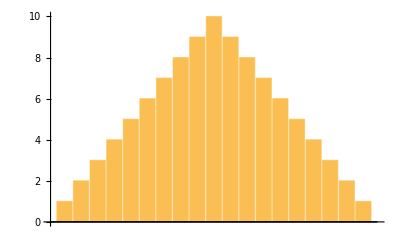
| Expected output: |  
  | -Graphics- |

Make a list of a pie chart, bar chart and line plot of the numbers from 1 to 10. »

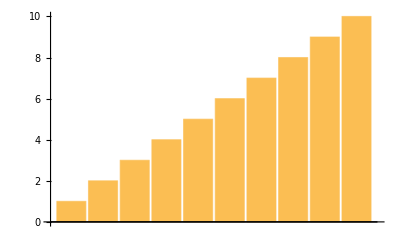
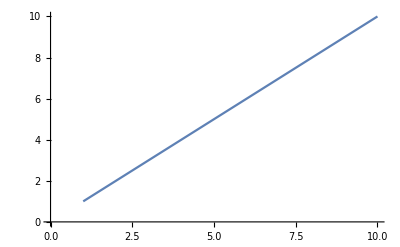
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Make a list of a pie chart and a bar chart of {1,1,2,3,5,8,13,21,34,55}. »

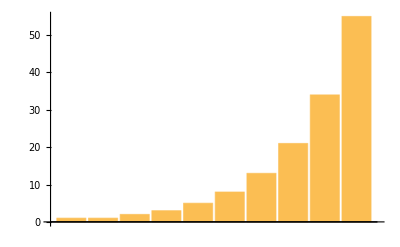
| Expected output: |  
  | {-Graphics-,-Graphics-} |

Make a column of two number line plots of {1,2,3,4,5}. »

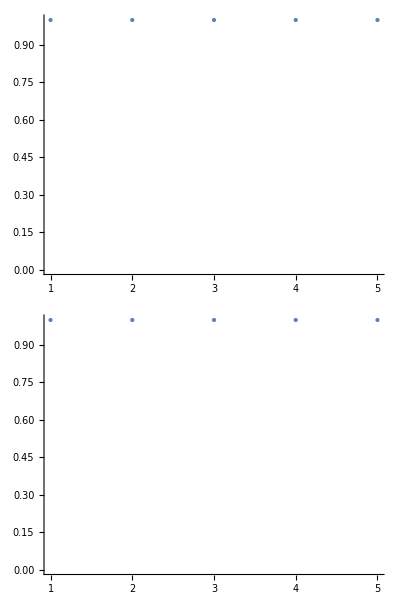
| Expected output: |  
  | -Graphics- |

Make a number line of fractions 1/2, 1/3, ... through 1/9. »

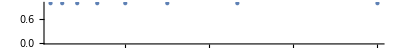
| Expected output: |  
  | -Graphics- |

Q&A

How do pie charts work in the Wolfram Language?

As in any pie chart, the wedges have relative sizes determined by the relative sizes of numbers in the list. In the Wolfram Language, the wedge for the first number starts at the 9 o’clock position, and then subsequent wedges read clockwise. The colors of the wedges are chosen in a definite sequence.

How is the vertical scale determined on plots?

It’s set up to automatically include all points except distant outliers. Later on (Section 20), we’ll talk about the PlotRange option, which lets you specify the exact range of the plot.

Tech Note

Particularly if you’re familiar with other computer languages, you may be surprised that a list of plots, for example, can appear as the output of a computation. This is made possible by the crucial fact that the Wolfram Language is symbolic. By the way, plots can appear in input as well.

More to Explore

Data Visualization in the Wolfram Language »

Charting and Information Visualization in the Wolfram Language »